```mathematica
$HistoryLength=0;ClearAll["Global`*"]; 
SetDirectory["/home/dan/ResearchLocal/tools"];
```

## Cos temp profile setup

```mathematica
Tratio=0.5
```

0.5

```mathematica
Tatm0=0.5;Tmid0=Tratio*Tatm0;zq0=2.0;δ=1.0;q=1.0;r=150;
```

```mathematica
Tatm=Tatm0(r/150)^q;Tmid=Tmid0(r/150)^q;zq=zq0(r/150)^1.3;
Tcos[z_]:=If[Abs[z]<zq,Tatm+(Tmid-Tatm)(Cos[(π z)/(2zq)])^(2δ),Tatm];
```

```mathematica
zq
```

2.

```mathematica
δ
```

1.

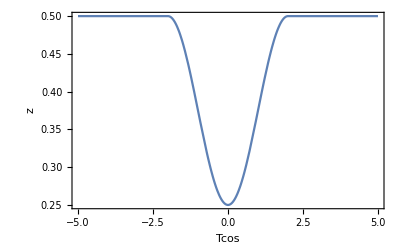

```mathematica
Plot[Tcos[z],{z,-5,5},PlotRange->Full,Frame->True,FrameLabel->{"Tcos","z"}]
```

## Solve for pressure and density profiles for cos temp profile and isothermal for comparison

```mathematica
P0=0.5;
```

```mathematica
sCos=NDSolve[{1/ρ[z] D[(Tcos[z]*ρ[z]), z]==-z,ρ[0]==P0/Tcos[0]},ρ[z],{z,0,5}];
ρCos[z_]:=Evaluate[ρ[z]/.sCos];
Pcos[z_]:=ρCos[z]*Tcos[z]
```

```mathematica
Tiso[z_]:=0.5;
sIso=NDSolve[{1/ρ[z] D[(Tiso[z]*ρ[z]), z]==-z,ρ[0]==P0/Tiso[0]},ρ[z],{z,0,5}];
ρIso[z_]:=Evaluate[ρ[z]/.sIso];
Piso[z_]:=ρIso[z]*Tiso[z]
```

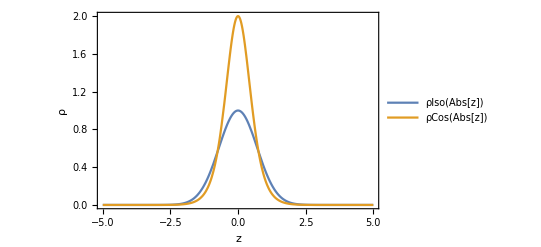

```mathematica
Plot[{ρIso[Abs[z]],ρCos[Abs[z]]},{z,-5,5},PlotLegends->"Expressions",Frame->True,FrameLabel->{"z","ρ"},ImageSize->"Large",PlotRange->Full]
```

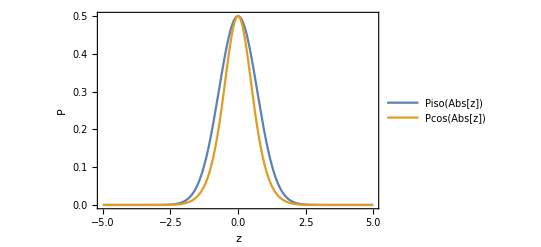

```mathematica
Plot[{Piso[Abs[z]],Pcos[Abs[z]]},{z,-5,5},PlotLegends->"Expressions",Frame->True,FrameLabel->{"z","P"},ImageSize->"Large"]
```

0.5+0.00151935 x3-1.03783 x3^2+0.373679 x3^3-0.688998 x3^4+6.55733 x3^5-15.4907 x3^6+19.9724 x3^7-16.9939 x3^8+10.2547 x3^9-4.50357 x3^10+1.4305 x3^11-0.311182 x3^12+0.0367956 x3^13+0.0019511 x3^14-0.00187676 x3^15+0.000422767 x3^16-0.0000554817 x3^17+4.54666×10^-6 x3^18-2.17254×10^-7 x3^19+4.65481×10^-9 x3^20

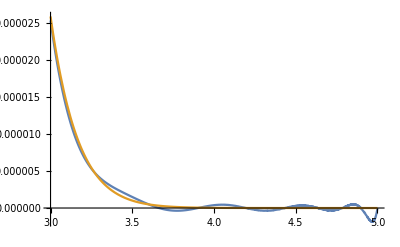

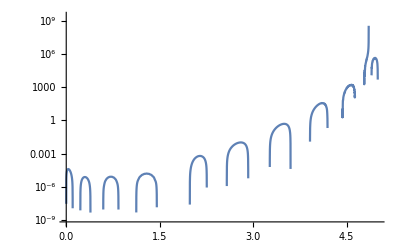

```mathematica
data=Table[{z,Pcos[z][[1]]},{z,0,5,0.1}];
fit=Fit[data,Table[x3^i,{i,0,20}],x3]
Plot[{fit,Pcos[x3]},{x3,3,5},PlotRange->Full]
LogPlot[{(fit-Pcos[x3])/Pcos[x3]},{x3,0,5},PlotRange->Full]
```

```mathematica
Plot[ρcos[
```

2.+0.0044661 x3-5.37199 x3^2+1.67665 x3^3-2.01248 x3^4+41.0936 x3^5-112.17 x3^6+159.33 x3^7-146.723 x3^8+94.8482 x3^9-44.3352 x3^10+14.9412 x3^11-3.45807 x3^12+0.44882 x3^13+0.014099 x3^14-0.0211508 x3^15+0.00508676 x3^16-0.000697833 x3^17+0.0000593599 x3^18-2.9332×10^-6 x3^19+6.4829×10^-8 x3^20

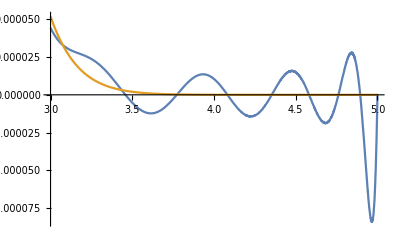

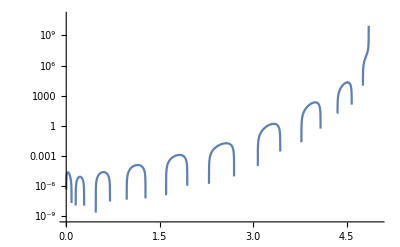

```mathematica
data=Table[{z,ρCos[z][[1]]},{z,0,5,0.1}];
fit=Fit[data,Table[x3^i,{i,0,20}],x3]
Plot[{fit,ρCos[x3]},{x3,3,5},PlotRange->Full]
LogPlot[{(fit-ρCos[x3])/ρCos[x3]},{x3,0,5},PlotRange->Full]
```